```mathematica
SetDirectory["/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete"]
fileList=FileNames["ph3_delay_01/*.txt"];
tot=24
dataDelay=Table[Import[fileList[[i+tot*(j-1)]],"Data"][[2;;All,1]],{i,1,tot},{j,1,tot}];
fileList=FileNames["ph3_delay_00/*.txt"];

dataSynch=Table[Import[fileList[[i+tot*(j-1)]],"Data"][[2;;All,1]],{i,1,tot},{j,1,tot}];
fileList=FileNames["ph3_delay_02/*.txt"];

dataAsynch=Table[Import[fileList[[i+tot*(j-1)]],"Data"][[2;;All,1]],{i,1,tot},{j,1,tot}];


(*fileList=FileNames["ph4_delay_03/*.txt"];
dataAdv=Table[Import[fileList[[i+tot*(j-1)]],"Data"][[2;;All,1]],{i,1,tot},{j,1,tot}];
*)
Dimensions[data]
```

/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete

24

{}

```mathematica
{If[data[[2,2,60]]>20,1,0],If[data[[2,2,140]]>20,1,0],If[data[[2,2,220]]>20,1,0]}
```

Part::partw: Part 60 of $Failed⟦2;;All,1⟧ does not exist.

Part::partw: Part 140 of $Failed⟦2;;All,1⟧ does not exist.

Part::partw: Part 220 of $Failed⟦2;;All,1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
isGatePh[dataSynch_,dataDelay_,dataAsynch_,thresh_]:=Block[{seg},
seg={If[Mean[dataSynch[[40;;All]]]>thresh,1,0],If[Mean[dataDelay[[40;;All]]]>thresh,1,0],If[Mean[dataDelay[[40;;All]]]>thresh,1,0],If[Mean[dataAsynch[[40;;All]]]>thresh,1,0]};
Piecewise[{
{1,seg=={1,1,1,1}},
{2,seg=={1,1,1,0}},
{3,seg=={0,1,1,0}},
{4,seg=={1,0,0,0}},
{5,seg=={0,1,1,1}},
{6,seg=={1,0,0,1}},
{7,seg=={0,0,0,1}},
{8,seg=={0,0,0,0}},
{9,seg=={0,1,0,0}},{10,seg=={0,0,1,0}},{11,seg=={1,0,1,1}},{12,seg=={1,1,0,1}}
}]
]


isGatePh2[dataSynch_,dataDelay_,dataAsynch_,dataAdv_,thresh_]:=Block[{seg},
seg={If[Mean[dataSynch[[40;;All]]]>thresh,1,0],If[Mean[dataDelay[[40;;All]]]>thresh,1,0],If[Mean[dataAdv[[40;;All]]]>thresh,1,0],If[Mean[dataAsynch[[40;;All]]]>thresh,1,0]};
Piecewise[{
{1,seg=={1,1,1,1}},
{2,seg=={1,1,1,0}},
{3,seg=={0,1,1,0}},
{4,seg=={1,0,0,0}},
{5,seg=={0,1,1,1}},
{6,seg=={1,0,0,1}},
{7,seg=={0,0,0,1}},
{8,seg=={0,0,0,0}},
{9,seg=={0,1,0,0}},{10,seg=={0,0,1,0}},{11,seg=={1,0,1,1}},{12,seg=={1,1,0,1}}
}]
]
dat=Table[isGatePh2[dataSynch[[i,j,50;;-1]],dataDelay[[i,j,50;;-1]],dataAsynch[[i,j,50;;-1]],dataDelay[[i,j,50;;-1]],0],{i,1,tot},{j,1,tot}]
```

{{8,8,8,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,1,1,5,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,3,6,1,5,5,5,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,1,5,5,1,1,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,1,7,7,1,5,1,1,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,5,6,1,6,1,5,5,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,1,6,7,1,7,5,1,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,7,8,7,6,5,5,5,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,7,3,5,1,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,3,5,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,3,8,3,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,2,1,2,1,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,5,4,5,2,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,3,2,1,2,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,1,1,1,1,1,1},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,6,8,6,2,1,1,1,1,1}}

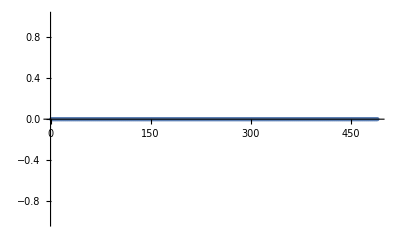

```mathematica
ListPlot[data[[20,20]]]
```

0.65

RGBColor[0.8, 0.1, 0.1]

RGBColor[0.9, 0.5, 0.2]

RGBColor[0.9, 0.8, 0.3]

RGBColor[0.1, 0.8, 0.4]

RGBColor[0.1, 0.4, 0.8]

RGBColor[0.7, 0.4, 0.8]

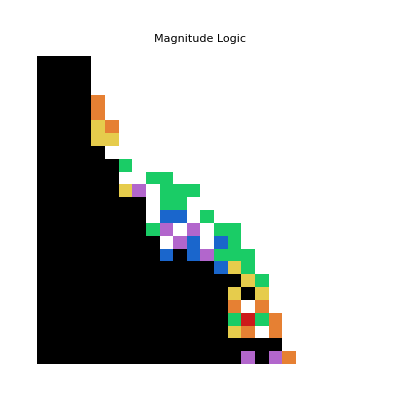

```mathematica
grey=.65
red = RGBColor[.8,.1,.1]
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.3]
green= RGBColor[.1,.8,.4]
blue =RGBColor[.1,.4,.8]
purple=RGBColor[.7,.4,.8]

ArrayPlot[dat,ColorRules->
{8->Black,1->White,4->red,2->orange,3->yellow,5->green,7->blue,6->purple,0->GrayLevel[grey],9->Pink,10->Pink,11->Cyan,12->Cyan,"NIMP1"->GrayLevel[grey],"NIMP2"->GrayLevel[grey],"AIMP1"->GrayLevel[grey],"AIMP2"->GrayLevel[grey],"XIMP1"->GrayLevel[grey],"XIMP2"->GrayLevel[grey],"IMP1"->GrayLevel[grey],"IMP2"->GrayLevel[grey]},PlotLegends->Automatic,DataRange->{{-1,5},{-1,5}},FrameTicks->Automatic,FrameLabel->{"Inhibitory Bias","Excitatory Bias"},PlotLabel->Style["Magnitude Logic","Title",Black,24]]
```

```mathematica
Dimensions[dataSynch]
```

{60,60,81}

```mathematica
Tan[Pi/4]
```

1

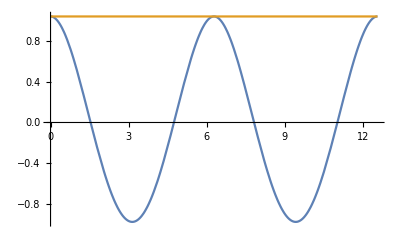

```mathematica
Plot[{Sum[Cos[n x]/(n^5),{n,1,100}],Zeta[5]},{x,0,4Pi}]
```

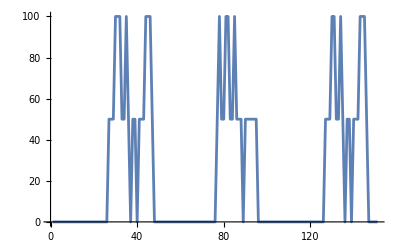

```mathematica
ListLinePlot[dataDelay[[14,11]]]
```

```mathematica
SetDirectory["/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete"]
fileList=FileNames["ph3_delay_01_V/*"];
tot=24
dataDelayV=Table[Import[fileList[[i+tot*(j-1)]],"Data"][[2;;All,1]],{i,1,tot},{j,1,tot}];
fileList=FileNames["ph3_delay_00_V/*"];
Print["ol'"]
dataSynchV=Table[Import[fileList[[i+tot*(j-1)]],"Data"][[2;;All,1]],{i,1,tot},{j,1,tot}];
fileList=FileNames["ph3_delay_02_V/*"];

dataAsynchV=Table[Import[fileList[[i+tot*(j-1)]],"Data"][[2;;All,1]],{i,1,tot},{j,1,tot}];
fileList=FileNames["ph3_delay_03_V/*"];
dataAdvV=Table[Import[fileList[[i+tot*(j-1)]],"Data"][[2;;All,1]],{i,1,tot},{j,1,tot}];
```

/media/alexander/9e1069d5-cd39-4e83-8eff-49b4335462dd/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete

24

ol'

3

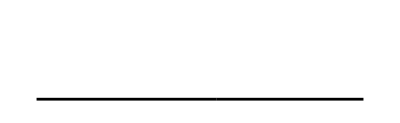

-Graphics-

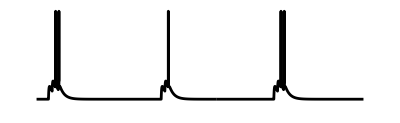

-Graphics-

```mathematica
a=6;b=3
ListLinePlot[dataSynchV[[a,b,500;;-1;;1]],PlotRange->{-.08,0},AspectRatio->1/GoldenRatio/2,Axes->None,PlotStyle->Black]
ListLinePlot[dataDelayV[[a,b,500;;-1;;1]],PlotRange->{-.08,0},AspectRatio->1/GoldenRatio/2,Axes->None,PlotStyle->Black]
ListLinePlot[dataAdvV[[a,b,500;;-1;;1]],PlotRange->{-.08,0},AspectRatio->1/GoldenRatio/2,Axes->None,PlotStyle->Black]
ListLinePlot[dataAsynchV[[a,b,500;;-1;;1]],PlotRange->{-.08,0},AspectRatio->1/GoldenRatio/2,Axes->None,PlotStyle->Black]
```

```mathematica
.. .
```

```mathematica
dat[[6]]
```

{8,8,10,10,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}